# dxy Exploration

## Dataset Load

```mathematica
dxyYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/NIRSdxy_yes_signal.mat"];
numSamplesDxyYes = Dimensions[dxyYesMatlab][[3]];
dxyYesRaw =  Table[Transpose[dxyYesMatlab[[1,1,x]]],{x,numSamplesDxyYes}];

dxyNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/NIRSdxy_no_signal.mat"];
numSamplesDxyNo = Dimensions[dxyNoMatlab][[3]];
dxyNoRaw =  Table[Transpose[dxyNoMatlab[[1,1,x]]],{x,numSamplesDxyNo}];

dxyDataFullYes = Table[dxyYesRaw[[x,All,All]]-> "Yes",{x,numSamplesDxyYes}];
dxyDataFullNo = Table[dxyNoRaw[[x,All,All]]-> "No",{x,numSamplesDxyNo}];

fullDataYesAndNoDxy = Join[dxyDataFullNo,dxyDataFullYes];

dxyYesRaw80={};
If[Dimensions[dxyYesRaw[[#]]][[2]]==81,AppendTo[dxyYesRaw80,Transpose@Drop[Transpose@dxyYesRaw[[#]],-1]], AppendTo[dxyYesRaw80,dxyYesRaw[[#]]]]&/@Range[numSamplesDxyYes];

dxyNoRaw80={};
If[Dimensions[dxyNoRaw[[#]]][[2]]==81,AppendTo[dxyNoRaw80,Transpose@Drop[Transpose@dxyNoRaw[[#]],-1]], AppendTo[dxyNoRaw80,dxyNoRaw[[#]]]]&/@Range[numSamplesDxyNo];
```

## Raw Data Visualization

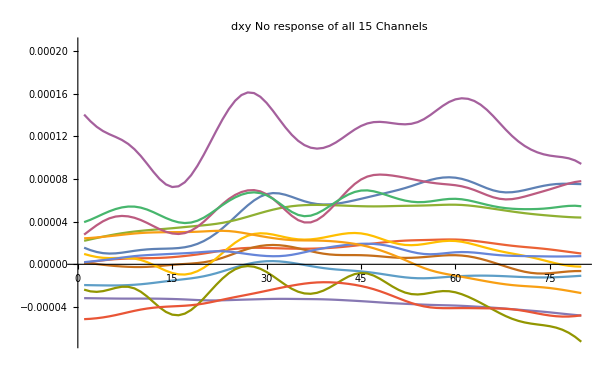

```mathematica
ListLinePlot[dxyNoRaw80[[1]],PlotLabel->"dxy No response of all 15 Channels"]
```

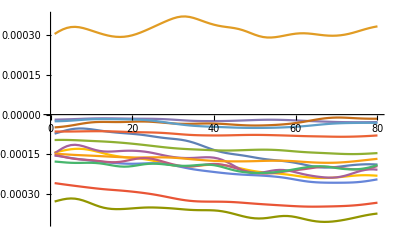
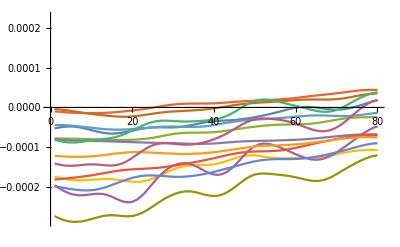
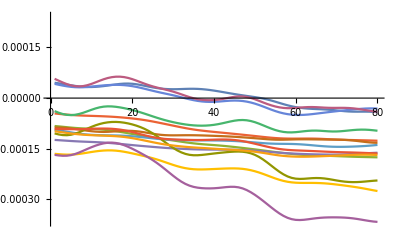
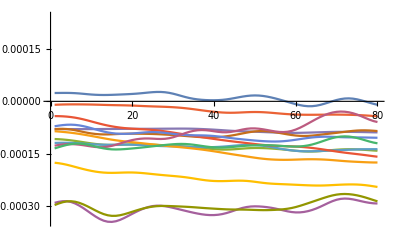
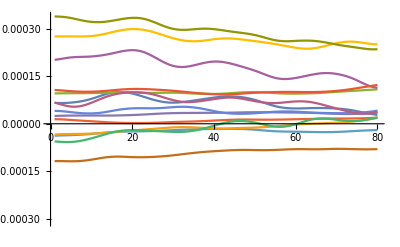
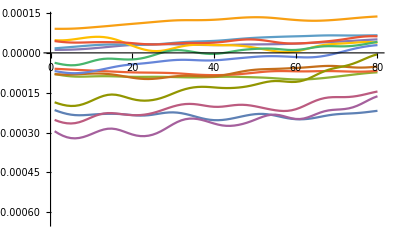

```mathematica
Table[ListLinePlot[dxyNoRaw80[[x]]],{x,2,7}]
```

## Dimensionality Reduction

#### Dimensionality Reduction on Channels

Dimensionality reduction of the channels performed via PCA

```mathematica
reducedDxyNo80 = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@dxyNoRaw80;
reducedDxyYes80 = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@dxyYesRaw80;
```

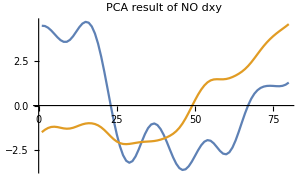

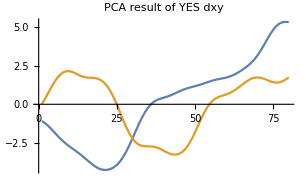

```mathematica
ListLinePlot[reducedDxyNo80[[1]],PlotLabel->"PCA result of NO dxy"]
ListLinePlot[reducedDxyYes80[[1]],PlotLabel->"PCA result of YES dxy"]
```

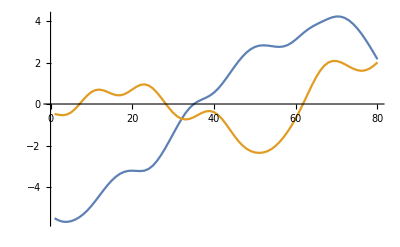
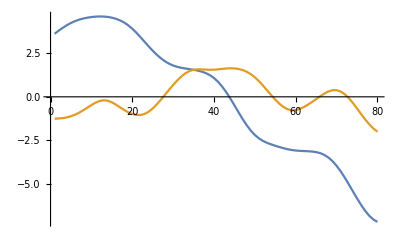
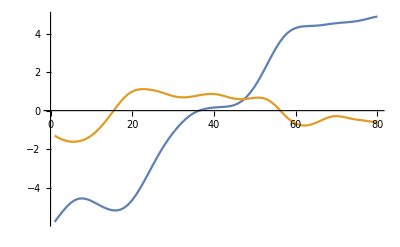
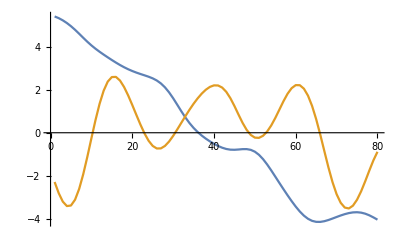
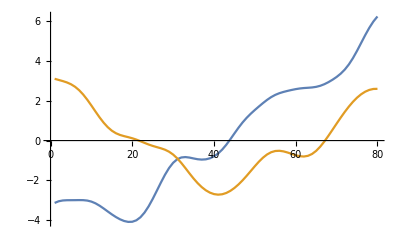
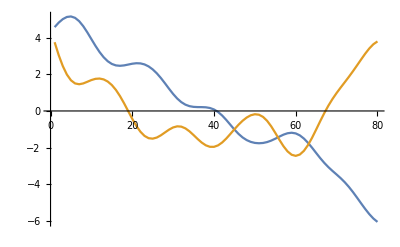

```mathematica
Table[ListLinePlot[reducedDxyNo80[[x]]],{x,2,7}]
```

## Dataset appearance of Principal Components

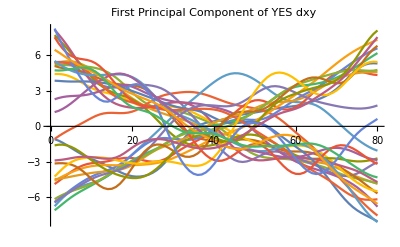

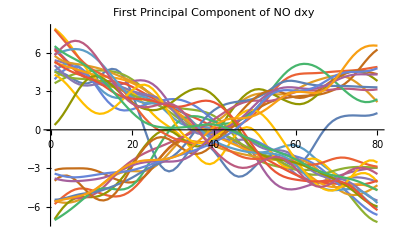

```mathematica
featYesDxyFirstComponent =Table[reducedDxyYes80[[x,1]],{x,30}];
featNoDxyFirstComponent  =Table[reducedDxyNo80[[x,1]],{x,30}];
ListLinePlot[featYesDxyFirstComponent,PlotLabel->"First Principal Component of YES dxy"]
ListLinePlot[featNoDxyFirstComponent,PlotLabel->"First Principal Component of NO dxy"]
```

## General Statistics

```mathematica
featExplore[f_]:=Histogram[{Legended[Table[f[reducedDxyNo80[[x,1]]],{x,30}],"No"],Legended[Table[f[reducedDxyYes80[[x,1]]],{x,30}],"Yes"]},PlotLabel->f]
```

```mathematica
energy=Total@(#^2)&;
stats={Mean,Median,RootMeanSquare,TrimmedMean,HarmonicMean,GeometricMean,ContraharmonicMean,Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange,Skewness,Kurtosis,QuartileSkewness,Entropy,energy};
```

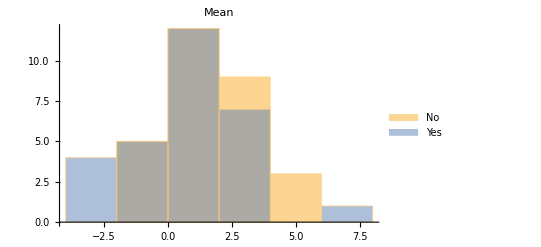
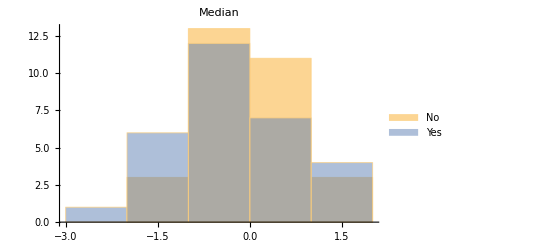
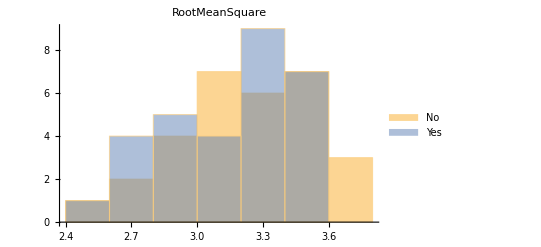
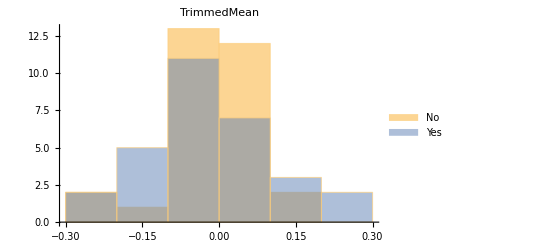
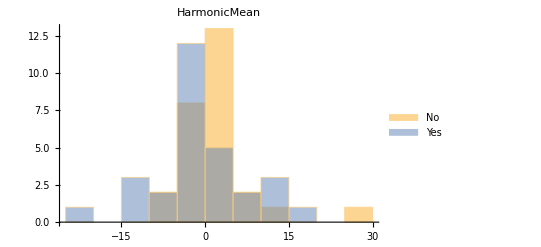
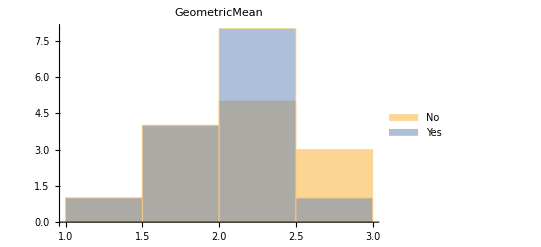
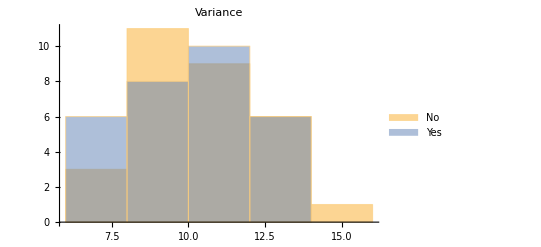
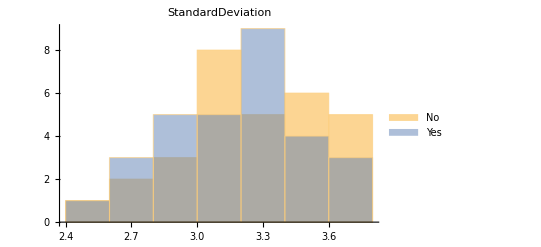
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[Style[featExplore[#],Larger]&/@stats]
```

### Frequency Transforms

### Frequency Transforms

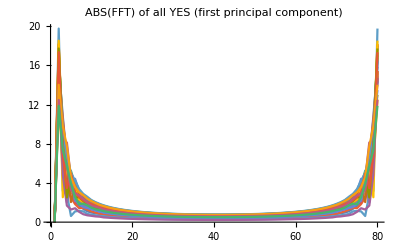

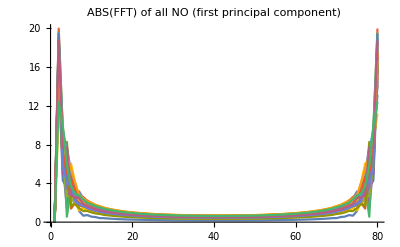

```mathematica
ListLinePlot[Table[Abs[Fourier[reducedDxyYes80[[x,1]] ]],{x,30}],PlotRange->All,PlotLabel->"ABS(FFT) of all YES (first principal component)"]
ListLinePlot[Table[Abs[Fourier[reducedDxyNo80[[x,1]] ]],{x,30}],PlotRange->All,PlotLabel->"ABS(FFT) of all NO (first principal component)"]
```

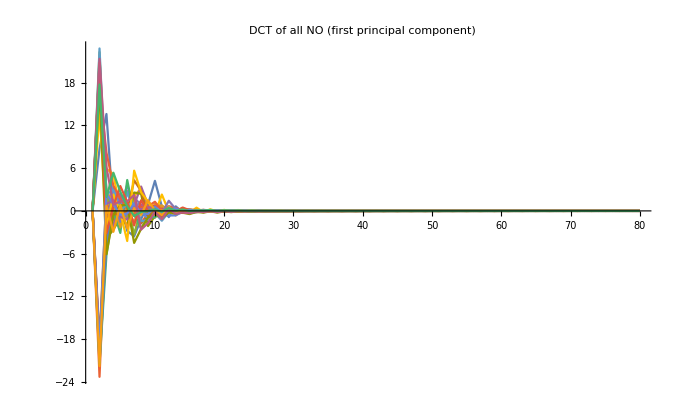

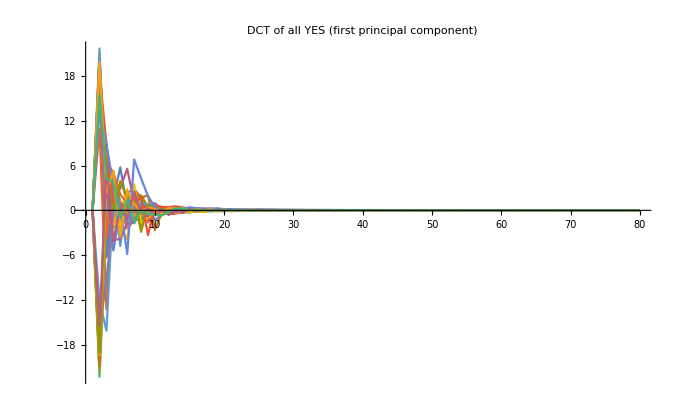

```mathematica
ListLinePlot[Table[FourierDCT[reducedDxyNo80[[x,1]] ],{x,30}],PlotRange->Full,PlotLabel->"DCT of all NO (first principal component)"]
ListLinePlot[Table[FourierDCT[reducedDxyYes80[[x,1]] ],{x,30}],PlotRange->Full,PlotLabel->"DCT of all YES (first principal component)"]
```